## Import astro

InterpolatingFunction[…]

2.62585×10^-10

0.

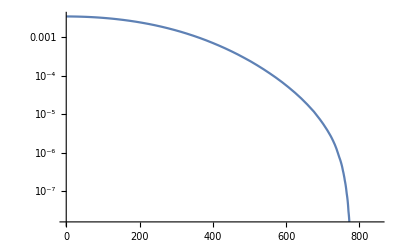

```mathematica
SetDirectory[NotebookDirectory[]];
Lgvmin=Import["../gvmin_round.dat"];
ResetDirectory[];
fgvmin=Interpolation[Lgvmin,InterpolationOrder->1]
fgvmin[794]
fgvmin[795]

LogPlot[fgvmin[vmin],{vmin,0,850}]
```

## Import fion

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

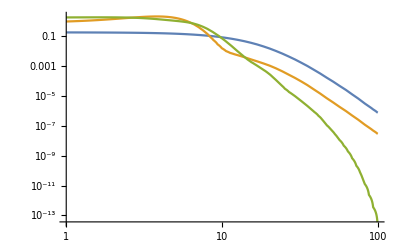

```mathematica
(*set path to form factor files*)
SetDirectory[NotebookDirectory[]<>"../../Formfactor_planewave"];
(*set path to form factor files*)

L1a=Import["CH4_1a_grid.dat"];
L2a=Import["CH4_2a_grid.dat"];
L1t=Import["CH4_1tx_grid.dat"];
ResetDirectory[];

f1a=Interpolation[L1a,InterpolationOrder->1]
f2a=Interpolation[L2a,InterpolationOrder->1]
f1t=Interpolation[L1t,InterpolationOrder->1]

LogLogPlot[{f1a[qx,0.02],f2a[qx,0.02],f1t[qx,0.02]},{qx,1,100}]
```

## Parameters

```mathematica
Params1a=Association[
wnl->2,
Inl->290.8,
Zeff->4.7,
fionnl->f1a
];

Params2a=Association[
wnl->2,
Inl->22.9,
Zeff->2.6,
fionnl->f2a
];

Params1t=Association[
wnl->6,
Inl->13.6,
Zeff->1.,
fionnl->f1t
];
```

## Rate calculation: FDM = 1

σe40 is the cross section relative to 10^-40 cm^2

#### dR/dE calculation: FDM = 1

```mathematica
TdRdE[mDMMeV0_,MNGeV0_,σe40_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];
Zeff1=Params1[Zeff];

ρ=0.3;(*GeV cm^-3*)
σe=10^-40 σe40a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

αEM=1/137.04;
pRMeV[ErkeV1_]:=Sqrt[2 meMeV ErkeV1 10^-3];
η1[ErkeV1_,Zeff_]:=Zeff αEM  meMeV/pRMeV[ErkeV1];
Ffermi[ErkeV_,Zeff_]:=2 Pi η1[ErkeV,Zeff]/(1-Exp[-2 Pi η1[ErkeV,Zeff]]);

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=  Ffermi[EekeV,Zeff1]ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM=1

```mathematica
TdRETotal[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1t],InterpolationOrder->1];

Ftot[x_]:=fσ1a[x]+fσ2a[x]+fσ1t[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

```mathematica
TdREComponents[mDMMeV0_,MNGeV0_,σe40_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe40a=σe40},

fσ1a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdE[mDMMeV,MNGeV,σe40a,Params1t],InterpolationOrder->1];

EikeV=0.001;
EfkeV=1.0;
steps=250;

T1=Table[{10^log10ErkeV,fσ1a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T2=Table[{10^log10ErkeV,fσ2a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T3=Table[{10^log10ErkeV,fσ1t[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

{T1,T2,T3}
]
```

### Calculate and Plot

```mathematica
ACH4=16.04;
MNGeV=ACH4 .931494; (*GeV*)
σ1=1; (*10^-40cm^2 cross section*)

TR30MeV=TdRETotal[30,MNGeV,σ1];
TR300MeV=TdRETotal[300,MNGeV,σ1];
TR1000MeV=TdRETotal[1000,MNGeV,σ1];

Tcomponents30MeV=TdREComponents[30,MNGeV,σ1];
Tcomponents300MeV=TdREComponents[300,MNGeV,σ1];
Tcomponents1000MeV=TdREComponents[1000,MNGeV,σ1];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_CH4_30MeV.dat",TR30MeV]
Export["dRdE_CH4_300MeV.dat",TR300MeV]
Export["dRdE_CH4_1000MeV.dat",TR1000MeV]
ResetDirectory[];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {23.9153}. NIntegrate obtained 2.50136 and 0.0000372884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {23.9318}. NIntegrate obtained 2.4837 and 0.0000511716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {28.7327}. NIntegrate obtained 2.46433 and 0.0000256841 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {185.55681904087}. NIntegrate obtained 0.0000462341 and 1.3951×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {185.576252412627}. NIntegrate obtained 0.0000461979 and 1.20504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {224.601}. NIntegrate obtained 0.0000461415 and 1.38772×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {167.0459035724205278938825358636677265167236328125}. NIntegrate obtained 0.0000365404 and 5.94208×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {167.0644948195359376086344127543270587921142578125}. NIntegrate obtained 0.0000365194 and 6.01799×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {167.08396239760997303847034345380961894989013671875}. NIntegrate obtained 0.0000364793 and 5.61655×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {23.9153}. NIntegrate obtained 2.50136 and 0.0000372884 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {23.9318}. NIntegrate obtained 2.4837 and 0.0000511716 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {28.7327}. NIntegrate obtained 2.46433 and 0.0000256841 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {185.55681904087}. NIntegrate obtained 0.0000462341 and 1.3951×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {185.576252412627}. NIntegrate obtained 0.0000461979 and 1.20504×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {224.601}. NIntegrate obtained 0.0000461415 and 1.38772×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {167.0459035724205278938825358636677265167236328125}. NIntegrate obtained 0.0000365404 and 5.94208×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {167.0644948195359376086344127543270587921142578125}. NIntegrate obtained 0.0000365194 and 6.01799×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {167.08396239760997303847034345380961894989013671875}. NIntegrate obtained 0.0000364793 and 5.61655×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

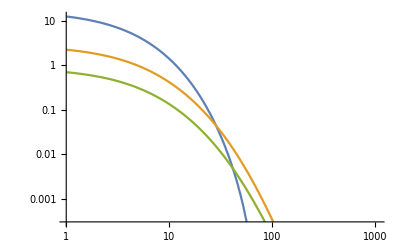

```mathematica
(*convert x-axis to eV*)
TR30MeV[[All,1]]=10^3 TR30MeV[[All,1]];
TR300MeV[[All,1]]=10^3 TR300MeV[[All,1]];
TR1000MeV[[All,1]]=10^3 TR1000MeV[[All,1]];


Show[ListLogLogPlot[{TR30MeV,TR300MeV,TR1000MeV},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

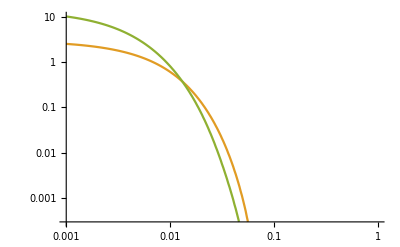

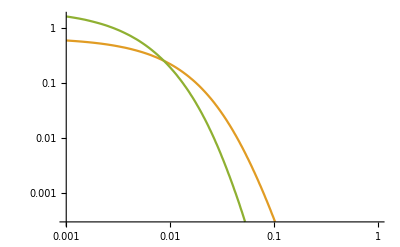

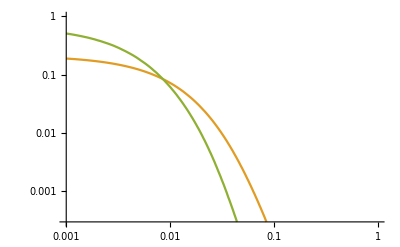

```mathematica
ListLogLogPlot[Tcomponents30MeV,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}}]
ListLogLogPlot[Tcomponents300MeV,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}}]
ListLogLogPlot[Tcomponents1000MeV,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}}]
```

## Rate calculation: FDM = (alpha me / q)^2

σe37 is the cross section relative to 10^-37 cm^2

#### dR/dE calculation: FDM = (alpha me / q)^2

```mathematica
TdRdElightmed[mDMMeV0_,MNGeV0_,σe37_,Params0_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37,Params1=Params0},

wnl1=Params1[wnl];
IeV1=Params1[Inl];
fion1=Params1[fionnl];
Zeff1=Params1[Zeff];

αEM=1/137.04;
ρ=0.3;(*GeV cm^-3*)
σe=10^-37 σe37a;(*cm^2*)
convert=4.355983 10^44;(*to convert from cm^-1 keV MeV^-3 km^-1 s to kg^-1 keV^-1 day^-1*)

meMeV=.510998928;(*MeV*)
mekeV=1000. meMeV;(*keV*)
μeMeV[mDM_]:=mDM meMeV /(meMeV +mDM);(*MeV*)

pRMeV[ErkeV1_]:=Sqrt[2 meMeV ErkeV1 10^-3];
η1[ErkeV1_,Zeff_]:=Zeff αEM  meMeV/pRMeV[ErkeV1];
Ffermi[ErkeV_,Zeff_]:=2 Pi η1[ErkeV,Zeff]/(1-Exp[-2 Pi η1[ErkeV,Zeff]]);

vmax=794;
ke[Eex0_]:=(2. meMeV Eex0)^0.5; (*returns momentum in keV (me MeV, Ee in eV)*)
KEmaxkeV[mDM0MeV_]:=0.5 mDM0MeV 10^3(vmax/(3 10^5))^2;
vmin[mDM0MeV_,Ee0eV_,q0keV_,I0eV_]:=Abs[(  q0keV/(2. mDM0MeV ) +(I0eV+Ee0eV)/q0keV  ) 300.];

qmaxkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1+Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];
qminkeV[mDM0MeV_,EekeV_,IkeV_]:=If[EekeV+IkeV<KEmaxkeV[mDM0MeV],mDM0MeV vmax/300(1-Sqrt[1- (EekeV+IkeV)/KEmaxkeV[mDM0MeV]]),0];

FDM[qkeV_]:=(αEM mekeV/qkeV)^2;

dRdEdq[mdmMeV_,qkeV_,EekeV_,IeV_,wnl_,fion_]:=   Ffermi[EekeV,Zeff1]FDM[qkeV]^2ρ/(MNGeV mdmMeV)wnl convert 1/EekeV  σe/(8 μeMeV[mdmMeV]^2)  qkeV fgvmin[vmin[mdmMeV,10^3 EekeV,qkeV,IeV]]fion[qkeV,EekeV];

EikeV=0.001;
EfkeV=1.0;
steps=150;

TdRdE1[mdmMeV_,IeV_,wnl_,fion_]:=Table[{10.^log10EkeV,
 NIntegrate[dRdEdq[mdmMeV,qx,10^log10EkeV,IeV,wnl,fion],{qx,qminkeV[mdmMeV,10^log10EkeV,IeV/1000.],qmaxkeV[mdmMeV,10^log10EkeV,IeV/1000.]},Method->{Automatic,"SymbolicProcessing"->False}]},{log10EkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

TRoutput=TdRdE1[mDMMeV,IeV1 ,wnl1,fion1]

]
```

#### dR/dE total calculation: FDM = (alpha me / q)^2

```mathematica
TdRETotallightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1t],InterpolationOrder->1];

Ftot[x_]:=fσ1a[x]+fσ2a[x]+fσ1t[x];

EikeV=0.001;
EfkeV=1.0;
steps=250;

Ttotal=Table[{10^log10ErkeV,Ftot[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}]
]
```

```mathematica
TdREComponentslightmed[mDMMeV0_,MNGeV0_,σe37_]:=Module[{mDMMeV=mDMMeV0,MNGeV=MNGeV0,σe37a=σe37},

fσ1a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1a],InterpolationOrder->1];
fσ2a=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params2a],InterpolationOrder->1];
fσ1t=Interpolation[TdRdElightmed[mDMMeV,MNGeV,σe37a,Params1t],InterpolationOrder->1];

EikeV=0.001;
EfkeV=1.0;
steps=250;

T1=Table[{10^log10ErkeV,fσ1a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T2=Table[{10^log10ErkeV,fσ2a[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];
T3=Table[{10^log10ErkeV,fσ1t[10^log10ErkeV]},{log10ErkeV,Log10[EikeV],Log10[EfkeV],(Log10[EfkeV]-Log10[EikeV])/steps}];

{T1,T2,T3}
]
```

### Calculate and Plot

```mathematica
ACH4=16.04;
MNGeV=ACH4 .931494; (*GeV*)
σ1=1; (*10^-37cm^2 cross section*)

TR30MeVlightmed=TdRETotallightmed[30,MNGeV,σ1];
TR300MeVlightmed=TdRETotallightmed[300,MNGeV,σ1];
TR1000MeVlightmed=TdRETotallightmed[1000,MNGeV,σ1];

Tcomponents30MeVlightmed=TdREComponentslightmed[30,MNGeV,σ1];
Tcomponents300MeVlightmed=TdREComponentslightmed[300,MNGeV,σ1];
Tcomponents1000MeVlightmed=TdREComponentslightmed[1000,MNGeV,σ1];

(*SetDirectory[NotebookDirectory[]];
Export["dRdE_CH4_30MeV_lightmed.dat",TR30MeVlightmed]
Export["dRdE_CH4_300MeV_lightmed.dat",TR300MeVlightmed]
Export["dRdE_CH4_1000MeV_lightmed.dat",TR1000MeVlightmed]
ResetDirectory[];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.7314754441966453413215276668779551982879638671875}. NIntegrate obtained 3.52235 and 0.0000785021 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.1677881122010429493229821673594415187835693359375}. NIntegrate obtained 3.47777 and 0.0000697721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {11.8365011985304675601327062395284883677959442138671875}. NIntegrate obtained 3.43036 and 0.0000450183 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {154.003679845974}. NIntegrate obtained 7.31932×10^-9 and 3.71103×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {140.966871634507}. NIntegrate obtained 7.30864×10^-9 and 3.733×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {144.649200726084}. NIntegrate obtained 7.29452×10^-9 and 3.60774×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {138.968072925336752376779259066097438335418701171875}. NIntegrate obtained 6.43503×10^-9 and 1.78273×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {138.986879021574278425532611436210572719573974609375}. NIntegrate obtained 6.42695×10^-9 and 1.85522×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {139.00657157605967739755215006880462169647216796875}. NIntegrate obtained 6.41589×10^-9 and 1.92892×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.7314754441966453413215276668779551982879638671875}. NIntegrate obtained 3.52235 and 0.0000785021 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {13.1677881122010429493229821673594415187835693359375}. NIntegrate obtained 3.47777 and 0.0000697721 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {11.8365011985304675601327062395284883677959442138671875}. NIntegrate obtained 3.43036 and 0.0000450183 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {154.003679845974}. NIntegrate obtained 7.31932×10^-9 and 3.71103×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {140.966871634507}. NIntegrate obtained 7.30864×10^-9 and 3.733×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {144.649200726084}. NIntegrate obtained 7.29452×10^-9 and 3.60774×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {138.968072925336752376779259066097438335418701171875}. NIntegrate obtained 6.43503×10^-9 and 1.78273×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {138.986879021574278425532611436210572719573974609375}. NIntegrate obtained 6.42695×10^-9 and 1.85522×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in qx near {qx} = {139.00657157605967739755215006880462169647216796875}. NIntegrate obtained 6.41589×10^-9 and 1.92892×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

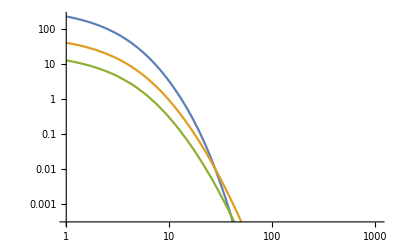

```mathematica
(*convert x-axis to eV*)
TR30MeVlightmed[[All,1]]=10^3 TR30MeVlightmed[[All,1]];
TR300MeVlightmed[[All,1]]=10^3 TR300MeVlightmed[[All,1]];
TR1000MeVlightmed[[All,1]]=10^3 TR1000MeVlightmed[[All,1]];


Show[ListLogLogPlot[{TR30MeVlightmed,TR300MeVlightmed,TR1000MeVlightmed},Joined->True,PlotRange->{{1,1070},{3 10^-4,Automatic}}]]
```

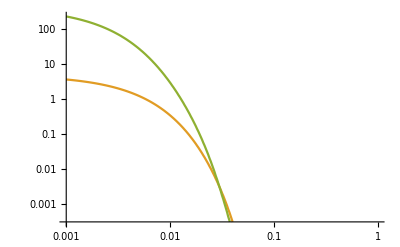

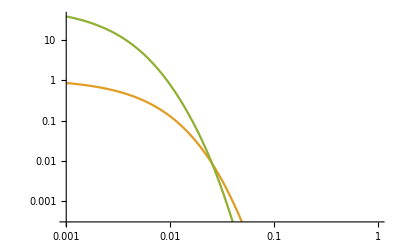

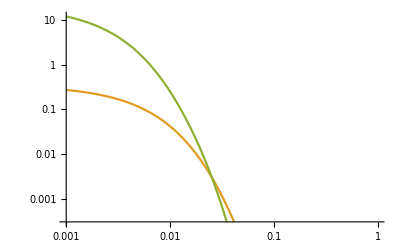

```mathematica
ListLogLogPlot[Tcomponents30MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}}]
ListLogLogPlot[Tcomponents300MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}}]
ListLogLogPlot[Tcomponents1000MeVlightmed,Joined->True,PlotRange->{{10^-3,1},{3 10^-4,Automatic}}]
```